```mathematica
ode=ψ'[x]+1/5 ψ[x]-ⅇ^(-x/5)Cos[x]==0
```

-ⅇ^(-x/5) Cos[x]+ψ[x]/5+ψ'[x]==0

```mathematica
generalSolution=FullSimplify[DSolve[ode,ψ[x],x]]
```

{{ψ[x]→ⅇ^(-x/5) (C[1]+Sin[x])}}

```mathematica
particularSolution=FullSimplify[DSolve[{ode,ψ[0]==0},ψ[x],x]]
```

{{ψ[x]→ⅇ^(-x/5) Sin[x]}}

```mathematica
ψa[x_]:=ψ[x]/.particularSolution[[1]]
```

```mathematica
FullSimplify[D[ψa[x],x]]
```

1/5 ⅇ^(-x/5) (5 Cos[x]-Sin[x])

```mathematica
dψadx[x_]:=1/5 ⅇ^(-x/5) (5 Cos[x]-Sin[x])
```

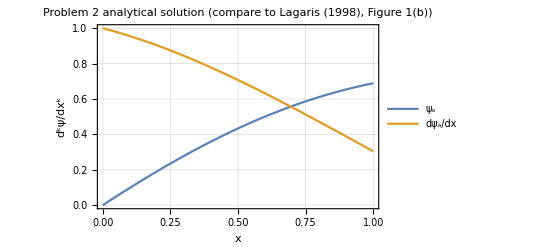

```mathematica
Plot[{ψa[x],dψadx[x]},{x,0,1},AxesLabel->{"x","d^kψ/dx^k"},PlotLegends->{"ψ_a","dψ_a/dx"},PlotLabel->"Problem 2 analytical solution (compare to Lagaris (1998), Figure 1(b))",Frame->True,GridLines->Automatic]
```